# Setup

```mathematica
(* ================================================================ *)
(* MODULE 0: SETUP                                                  *)
(* ================================================================ *)

baseDir = NotebookDirectory[];
Get[FileNameJoin[{baseDir, "QKT_full.wl"}]];
$HistoryLength = 0;
EnsureDir[dir_] := If[!DirectoryQ[dir],
  CreateDirectory[dir, CreateIntermediateDirectories -> True]];
kStr[k_] := StringReplace[
  If[StringEndsQ[#, "."], # <> "0", #] &[ToString[N[k]]], "." -> "_"];
```

```mathematica
LaunchKernels[14];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

# QKT functions used

```mathematica
Clear[GetQKTParityEigensystem];
GetQKTParityEigensystem[jParam_, alphaParam_, kParam_,theta_] :=
  Module[{d=2 jParam + 1,mat, idx, matEven, matOdd, esEven, esOdd,phEven, phOdd, vecsEven, vecsOdd, idxE, idxO,fullVecsEven, fullVecsOdd,D},

(*2. Symmetric Floquet operator in Jz basis*)
D=DiagonalMatrix[Exp[-I theta Range[jParam, -jParam, -1]]];
mat =D. Floqsym[jParam, alphaParam, kParam].ConjugateTranspose[D];

idx = ParitySectorIndices[jParam];
    matEven = mat[[idx["Even"], idx["Even"]]];
    matOdd  = mat[[idx["Odd"], idx["Odd"]]];
    esEven = Eigensystem[matEven, Method -> "Direct"];
    esOdd  = Eigensystem[matOdd, Method -> "Direct"];
    phEven = Mod[Arg[esEven[[1]]], 2 Pi];
    phOdd  = Mod[Arg[esOdd[[1]]], 2 Pi];

idxE = Ordering[phEven];
idxO = Ordering[phOdd];
vecsEven = esEven[[2, idxE]];
vecsOdd  = esOdd[[2, idxO]];
fullVecsEven = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Even"]]] = vecsEven[[i]]; vec],
      {i, Length[idx["Even"]]}];

    fullVecsOdd = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Odd"]]] = vecsOdd[[i]]; vec],
      {i, Length[idx["Odd"]]}];

    <|"Even" -> <|"Quasienergies" -> esEven[[1]],
                  "Phases" -> phEven,
                  "Vectors" -> vecsEven,
                  "FullVectors" -> fullVecsEven|>,
      "Odd"  -> <|"Quasienergies" -> esOdd[[1]], 
                  "Phases" -> phOdd,
                  "Vectors" -> vecsOdd,
                  "FullVectors" -> fullVecsOdd|>|>
  ]
```

# Parameters

```mathematica
(* ================================================================ *)
(* MODULE 1: PARAMETERS                                             *)
(* ================================================================ *)

J       = 300;
alpha   = 0.84;
kCenter = 15.;
delta   = 0.01;
nQKT    = 10;
nCOE    = 50;

(* --- Directories --- *)
runLabel = "J" <> ToString[J] <> "_k" <> kStr[kCenter];
resultsDir = FileNameJoin[{baseDir, "Results", runLabel}];
evenDir    = FileNameJoin[{resultsDir, "Even"}];
oddDir     = FileNameJoin[{resultsDir, "Odd"}];
plotDir    = FileNameJoin[{resultsDir, "plots"}];
collageDir = FileNameJoin[{resultsDir, "individual"}];
EnsureDir[evenDir]; EnsureDir[oddDir];
EnsureDir[plotDir]; EnsureDir[collageDir];

(* --- Plot style --- *)
$pOpts = Sequence[ImageSize -> 800, Frame -> True,
  FrameStyle -> Directive[Black, 25],
  LabelStyle -> Directive[Black, 25]];
$cOpts = Sequence[Frame -> True,
  FrameStyle -> Directive[Black, 16],
  LabelStyle -> Directive[Black, 16]];
$cSize = 380;
$legStyle = Directive[Black, 18];

SavePlot[plt_, name_] := (
  Export[FileNameJoin[{plotDir, name <> ".png"}],
    Rasterize[plt, ImageResolution -> 150, Background -> White]];
  Print["  Saved: ", name, ".png"]);
```

# Method

```mathematica
(* --- Generate --- *)
  Print["=== GENERATING QKT ENSEMBLE ==="];
(*  SeedRandom[42];*)
  kList = RandomReal[{kCenter - delta, kCenter + delta}, nQKT];
  {tGen, qktEnsemble} = AbsoluteTiming[
    GenerateQKTEnsemble[J, alpha, kList]];
  Print["  ", nQKT, " matrices done in ", Round[tGen, 0.1], "s"];
  Export[FileNameJoin[{evenDir, "spectra_k"<>ToString[kCenter]<>".wdx"}], qktEnsemble["Even"], "WDX"];
  Export[FileNameJoin[{oddDir, "spectra_k"<>ToString[kCenter]<>".wdx"}], qktEnsemble["Odd"], "WDX"];
  Print["  Spectra exported"];
```

=== GENERATING QKT ENSEMBLE ===

10 matrices done in 6.1s

Spectra exported

```mathematica
(* --- Import --- *)
(*qktEnsemble = <|
    "Even" -> Import[FileNameJoin[{evenDir, "spectra.wdx"}]],
    "Odd"  -> Import[FileNameJoin[{oddDir, "spectra.wdx"}]]|>;
  If[FailureQ[qktEnsemble["Even"]] || FailureQ[qktEnsemble["Odd"]],
    Print["ERROR: Import failed. Check paths."]; Abort[]];
  Print["  Imported successfully"];*)
  qktEnsemble = <|
    "Even" -> Import["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\Results\\J500_k27_5\\Even\\spectra_k27.5.wdx"],
    "Odd"  -> Import["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\Results\\J500_k27_5\\Odd\\spectra_k27.5.wdx"]|>;

  If[FailureQ[qktEnsemble["Even"]] || FailureQ[qktEnsemble["Odd"]],
    Print["ERROR: Import failed. Check paths."]; Abort[]];
  Print["  Imported successfully"];
```

Imported successfully

```mathematica
dimE = qktEnsemble["Even"][[1]]["N"];
dimO = qktEnsemble["Odd"][[1]]["N"];
nReal = Length[qktEnsemble["Even"]];
Print["  Even N=", dimE, ", Odd N=", dimO, ", nReal=", nReal];
```

Even N=Even[N], Odd N=Odd[N], nReal=1

# SFF

```mathematica
EnsembleSFFFull[spectraList_List,tauMax_Real,nPts_Integer]:=Module[{nMat,taus,specArray,allK},
nMat=Length[spectraList];
taus=N[Range[1,nPts] (tauMax/nPts)];
specArray=Map[#["Spectrum"]&,spectraList];
DistributeDefinitions[CompileSFF,taus,specArray];
allK=ParallelTable[CompileSFF[specArray[[i]],taus],{i,nMat},Method->"CoarsestGrained"];
<|"Tau"->taus,"AllK"->allK,"MeanK"->Mean[allK],"SE"->StandardDeviation[allK]/Sqrt[nMat*1.]|>];
SmoothSFF[kVec_List,tauVec_List,sigmaTau_?NumericQ]:=GaussianFilter[kVec,sigmaTau/(tauVec[[2]]-tauVec[[1]])];
```

## method

```mathematica
tauMaxSFF=3.0;
nPtsSFF=10000;
sigmaSm=0.01;

sffEven=EnsembleSFFFull[qktEnsemble["Even"],tauMaxSFF,nPtsSFF];
sffOdd=EnsembleSFFFull[qktEnsemble["Odd"],tauMaxSFF,nPtsSFF];
sffCOE=EnsembleSFFFull[coeSpectra,tauMaxSFF,nPtsSFF];

tauGrid=sffEven["Tau"];

(*Smooth each realization individually,then take the mean of the smoothed curves*)
kEvenAllSm=Map[SmoothSFF[#,tauGrid,sigmaSm]&,sffEven["AllK"]];
kOddAllSm=Map[SmoothSFF[#,tauGrid,sigmaSm]&,sffOdd["AllK"]];
kCOEAllSm=Map[SmoothSFF[#,tauGrid,sigmaSm]&,sffCOE["AllK"]];

kEvenMeanSm=Mean[kEvenAllSm];
kOddMeanSm=Mean[kOddAllSm];
kCOEMeanSm=Mean[kCOEAllSm];

kCOEAn=Map[COESFFAnalytical,tauGrid];
```

## plotting

```mathematica
(*Pick one representative realization for the "individual" panel*)
iShow=1;

plotIndiv=ListLinePlot[{Transpose[{tauGrid,sffEven["AllK"][[iShow]]}],Transpose[{tauGrid,kEvenAllSm[[iShow]]}]},PlotStyle->{Directive[Thin,Gray],Directive[Thick,RGBColor[0.2,0.4,0.8]],Directive[Thick,Dashed,Red]},PlotLegends->{"raw K_i","smoothed K_i","COE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Single realization (Even sector, i="<>ToString[iShow]<>")",ImageSize->700]
```

-Graphics-

```mathematica
plotEnsemble=ListLinePlot[{Transpose[{tauGrid,kEvenMeanSm}],Transpose[{tauGrid,kOddMeanSm}],Transpose[{tauGrid,kCOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.2,0.4,0.8]],Directive[Thick,RGBColor[0.8,0.3,0.2]],Directive[Thick,RGBColor[0.3,0.6,0.3]],Directive[Thick,Dashed,Red]},PlotLegends->{"Even smoothed mean","Odd smoothed mean","COE","COE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF, J = "<>ToString[J]<>", k = "<>ToString[kCenter]<>", m = "<>ToString[nQKT],ImageSize->700,LabelStyle->Directive[Black,20]]
```

-Graphics-

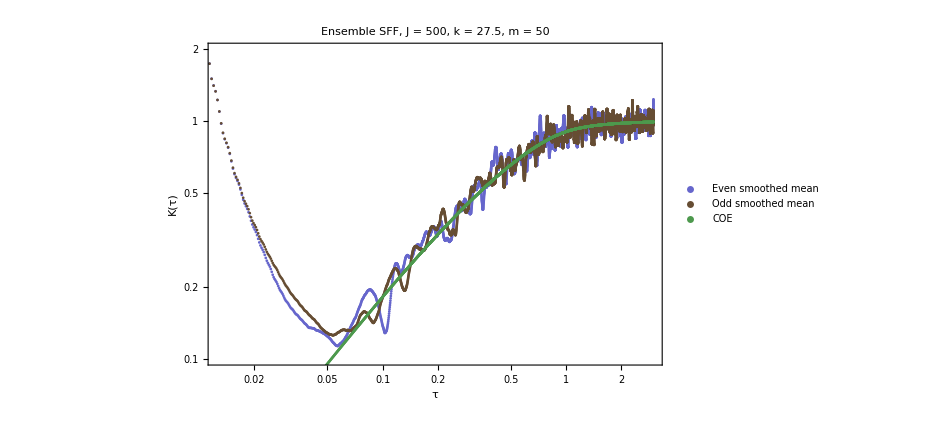

```mathematica
plot400=ListLogLogPlot[{Transpose[{tauGrid,kEvenMeanSm}],Transpose[{tauGrid,kOddMeanSm}],Transpose[{tauGrid,kCOEAn}]},PlotStyle->{Directive[Thick,RGBColor[0.4,0.4,0.8]],Directive[Thick,RGBColor[0.4,0.3,0.2]],Directive[Thick,RGBColor[0.3,0.6,0.3]],Directive[Thick,Dashed,Red]},PlotLegends->{"Even smoothed mean","Odd smoothed mean","COE","COE analytical"},Frame->True,FrameLabel->{"τ","K(τ)"},PlotLabel->"Ensemble SFF, J = "<>ToString[J]<>", k = "<>ToString[kCenter]<>", m = "<>ToString[nQKT],ImageSize->700,LabelStyle->Directive[Black,20],PlotRange->{{0.0125,3},{0.1,2}}]
```

# New Texture

```mathematica
Clear[GetQKTParityEigensystem];
GetQKTParityEigensystem[jParam_, alphaParam_, kParam_,theta_] :=
  Module[{d=2 jParam + 1,mat, idx, matEven, matOdd, esEven, esOdd,phEven, phOdd, vecsEven, vecsOdd, idxE, idxO,fullVecsEven, fullVecsOdd,D},

(*2. Symmetric Floquet operator in Jz basis*)
D=DiagonalMatrix[Exp[-I theta Range[jParam, -jParam, -1]]];
mat =D. Floqsym[jParam, alphaParam, kParam].ConjugateTranspose[D];

idx = ParitySectorIndices[jParam];
    matEven = mat[[idx["Even"], idx["Even"]]];
    matOdd  = mat[[idx["Odd"], idx["Odd"]]];
    esEven = Eigensystem[matEven, Method -> "Direct"];
    esOdd  = Eigensystem[matOdd, Method -> "Direct"];
    phEven = Mod[Arg[esEven[[1]]], 2 Pi];
    phOdd  = Mod[Arg[esOdd[[1]]], 2 Pi];

idxE = Ordering[phEven];
idxO = Ordering[phOdd];
vecsEven = esEven[[2, idxE]];
vecsOdd  = esOdd[[2, idxO]];
fullVecsEven = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Even"]]] = vecsEven[[i]]; vec],
      {i, Length[idx["Even"]]}];

    fullVecsOdd = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Odd"]]] = vecsOdd[[i]]; vec],
      {i, Length[idx["Odd"]]}];

    <|"Even" -> <|"Quasienergies" -> esEven[[1]],
                  "Phases" -> phEven,
                  "Vectors" -> vecsEven,
                  "FullVectors" -> fullVecsEven|>,
      "Odd"  -> <|"Quasienergies" -> esOdd[[1]], 
                  "Phases" -> phOdd,
                  "Vectors" -> vecsOdd,
                  "FullVectors" -> fullVecsOdd|>|>
  ]
```

```mathematica
(* ============================================================ *)
(* ENSEMBLE TEXTURE FUNCTION                                     *)
(* ============================================================ *)
Clear[EnsembleTexFull];
EnsembleTexFull[ensembleList_List, tMax_Integer] :=
  Module[{nMat = Length[ensembleList], tGrid = Range[0, tMax],
          allFull, allDiag, allOffDiag},
    Print["Processing ", nMat, " realizations up to t = ", tMax, "..."];
    DistributeDefinitions[tGrid];
    {allFull, allDiag} = Transpose@ParallelTable[
      Module[{phases, vecs, d, f1, pArray, diagPart, fullTex},
        phases   = ensembleList[[i, "Phases"]];
        vecs     = ensembleList[[i, "Vectors"]];
        d        = Length[phases];
        f1       = N@ConstantArray[1/Sqrt[d], d];
        pArray   = Abs[Conjugate[vecs] . f1]^2;
        diagPart = d * Total[pArray^2];
        fullTex  = Table[d * Abs[Total[pArray * Exp[-I t phases]]]^2, {t, tGrid}];
        {fullTex, ConstantArray[diagPart, Length[tGrid]]}
      ], {i, nMat}, Method -> "CoarsestGrained"];
    allOffDiag = allFull - allDiag;
    <|"Time"       -> tGrid,
      "AllTex"     -> allFull,     (* backward compat *)
      "AllFull"    -> allFull,     "MeanFull"    -> Mean[allFull],
      "AllDiag"    -> allDiag,     "MeanDiag"    -> Mean[allDiag],
      "AllOffDiag" -> allOffDiag,  "MeanOffDiag" -> Mean[allOffDiag]|>];
```

```mathematica
(* ============================================================ *)
(* PARAMETERS + ENSEMBLE GENERATION                             *)
(* ============================================================ *)
nQKT    = 50;
J       = 300;
α       = 0.84;
θ=α/2;
kCenter = 15.;
δ       = 0.01;
kList   = RandomReal[{kCenter - δ, kCenter + δ}, nQKT];

Print["Generating ", nQKT, " matrices..."];
rawEnsembleData = ParallelTable[
  GetQKTParityEigensystem[J, α, k,θ], {k, kList},
  Method -> "CoarsestGrained"];

qktEnsemble = <|
  "Even" -> Table[<|"Phases"  -> Arg[data["Even", "Quasienergies"]],
                    "Vectors" -> data["Even", "Vectors"]|>, {data, rawEnsembleData}],
  "Odd"  -> Table[<|"Phases"  -> Arg[data["Odd",  "Quasienergies"]],
                    "Vectors" -> data["Odd",  "Vectors"]|>, {data, rawEnsembleData}]|>;
```

Generating 50 matrices...

```mathematica
(*COMPUTE TEXTURE*)
tMaxTex = 2000;
sigmaSm = 5;

Print["Computing Even Sector..."];
texEven = EnsembleTexFull[qktEnsemble["Even"], tMaxTex];
Print["Computing Odd Sector..."];
texOdd  = EnsembleTexFull[qktEnsemble["Odd"],  tMaxTex];
```

Computing Even Sector...

Processing 50 realizations up to t = 2000...

Computing Odd Sector...

Processing 50 realizations up to t = 2000...

```mathematica
tGrid = texEven["Time"];
(* SMOOTH *)
texEvenAllSm  = Map[GaussianFilter[#, sigmaSm] &, texEven["AllFull"]];
texOddAllSm   = Map[GaussianFilter[#, sigmaSm] &, texOdd["AllFull"]];
texEvenMeanSm = Mean[texEvenAllSm];
texOddMeanSm  = Mean[texOddAllSm];
(* Diagonal and off-diagonal smoothed means *)
texEvenDiagSm   = Mean[Map[GaussianFilter[#, sigmaSm] &, texEven["AllDiag"]]];
texOddDiagSm    = Mean[Map[GaussianFilter[#, sigmaSm] &, texOdd["AllDiag"]]];
texEvenOffDSm   = Mean[Map[GaussianFilter[#, sigmaSm] &, texEven["AllOffDiag"]]];
texOddOffDSm    = Mean[Map[GaussianFilter[#, sigmaSm] &, texOdd["AllOffDiag"]]];
```

```mathematica
(* ============================================================ *)
(* PLOT 1: Single realization                                    *)
(* ============================================================ *)
iShow = 1;
plotIndivTex = ListLinePlot[
  {Transpose[{tGrid, texEven["AllTex"][[iShow]]}],
   Transpose[{tGrid, texEvenAllSm[[iShow]]}]},
  PlotStyle   -> {Directive[Thin, Gray], Directive[Thick, RGBColor[0.2, 0.4, 0.8]]},
  PlotLegends -> {"raw tex_i", "smoothed tex_i"},
  Frame -> True, FrameLabel -> {"t (kicks)", "Σ(t)"},
  PlotLabel -> "Single Realization (Even, i=" <> ToString[iShow] <> ")",
  ImageSize -> 700, LabelStyle -> Directive[Black, 16]]
```

```mathematica
(* ============================================================ *)
(* PLOT 2: Ensemble mean full                                    *)
(* ============================================================ *)
plotMeanTex = ListLinePlot[
  {Transpose[{tGrid, texEvenMeanSm}],
   Transpose[{tGrid, texOddMeanSm}]},
  PlotStyle   -> {Directive[Thick, Blue], Directive[Thick, Red]},
  PlotLegends -> {"Even", "Odd"},
  Frame -> True, FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  PlotLabel -> "QKT Texture  J = " <> ToString[J] <>
               "  k = " <> ToString[kCenter] <>
               "  M = " <> ToString[nQKT],
  ImageSize -> 700, LabelStyle -> Directive[Black, 16],
  PlotRange -> {All, {0,5}}]
```

```mathematica
(* ============================================================ *)
(* PLOT 3: Diagonal vs off-diagonal vs full (even sector)       *)
(* ============================================================ *)
plotDecomp = ListLinePlot[
  {Transpose[{tGrid, texEvenMeanSm}],
   Transpose[{tGrid, texEvenDiagSm}],
   Transpose[{tGrid, texEvenOffDSm}]},
  PlotStyle   -> {Directive[Thick, Blue],
                  Directive[Thick, Red],
                  Directive[Thick, Green]},
  PlotLegends -> {"Full Σ(t)", "Diagonal d∑Pₖ.b2", "Off-diagonal"},
  Frame -> True, FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  PlotLabel -> "Texture Decomposition (Even sector)",
  GridLines -> {None, {2, 3}},
  ImageSize -> 700, LabelStyle -> Directive[Black, 16]]
```

```mathematica
plotDecomp = ListLinePlot[
  {Transpose[{tGrid, texOddMeanSm}],
   Transpose[{tGrid, texOddDiagSm}],
   Transpose[{tGrid, texOddOffDSm}]},
  PlotStyle   -> {Directive[Thick, Blue],
                  Directive[Thick, Red],
                  Directive[Thick, Green]},
  PlotLegends -> {"Full Σ(t)", "Diagonal d∑Pₖ.b2", "Off-diagonal"},
  Frame -> True, FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  PlotLabel -> "Texture Decomposition (Odd sector)",
  GridLines -> {None, {2, 3}},
  ImageSize -> 700, LabelStyle -> Directive[Black, 16]]
```

```mathematica
ListLinePlot[
  {Transpose[{tGrid, texEvenOffDSm}],
   Transpose[{tGrid, texOddOffDSm}]},
  PlotStyle   -> {Directive[Thick, Blue],
                  Directive[Thick, Red],
                  Directive[Thick, Green]},
  PlotLegends -> {"Full Σ(t)", "Diagonal d∑Pₖ.b2", "Off-diagonal"},
  Frame -> True, FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  PlotLabel -> "Texture Decomposition (Odd sector)",
  GridLines -> {None, {2, 3}},
  ImageSize -> 700, LabelStyle -> Directive[Black, 16],
PlotRange->{All,{-1.2,1}}]
```

# Tests

```mathematica
(* ============================================================ *)
(*  TEXTURE WITH BUILT-IN ROTATION — no separate rotateEnsemble *)
(* ============================================================ *)
Clear[EnsembleTexTheta];
EnsembleTexTheta[baseList_List, mVals_List, theta_Real, tMax_Integer] :=
  Module[{nMat = Length[baseList], tGrid = Range[0, tMax],
          allFull, allDiag, allOffDiag},
    DistributeDefinitions[tGrid, baseList, mVals, theta];
    {allFull, allDiag} = Transpose@ParallelTable[
      Module[{phases, vecs, d, f1, pArray, diagPart, fullTex, ph},
        phases = baseList[[i, "Phases"]];
        vecs   = baseList[[i, "Vectors"]];   (* real, from theta=0 *)
        d      = Length[phases];
        (* Rotate: multiply component m by Exp[-I theta mVals[[m]]] *)
        ph     = Exp[-I theta mVals];
        f1     = ph / Sqrt[d];               (* phase-twisted probe *)
        pArray = Abs[vecs . f1]^2;           (* P_k for this theta *)
        diagPart = d * Total[pArray^2];
        fullTex  = Table[d * Abs[Total[pArray * Exp[-I t phases]]]^2,
                         {t, tGrid}];
        {fullTex, ConstantArray[diagPart, Length[tGrid]]}
      ], {i, nMat}, Method -> "CoarsestGrained"];
    allOffDiag = allFull - allDiag;
    <|"Time" -> tGrid,
      "AllTex"     -> allFull,
      "AllFull"    -> allFull,    "MeanFull"    -> Mean[allFull],
      "AllDiag"    -> allDiag,    "MeanDiag"    -> Mean[allDiag],
      "AllOffDiag" -> allOffDiag, "MeanOffDiag" -> Mean[allOffDiag]|>];

(*  SMOOTHER                                                     *)
sm[curves_] := Mean[Map[GaussianFilter[#, sigmaSm] &, curves]];
```

```mathematica
(*  PLOT BUILDER  *)
```

```mathematica
makePlots[texE_, texO_, tGrid_, theta_, nMat_] :=
  Module[{tStr, texEsm, texOsm, texEDiag, texODiag, texEOff, texOOff,
          p1, p2, p3, p4, style},
    tStr = "θ/π = " <> ToString[NumberForm[N[theta/Pi], {4, 3}]];

    texEsm   = sm[texE["AllFull"]];    texOsm   = sm[texO["AllFull"]];
    texEDiag = sm[texE["AllDiag"]];    texODiag = sm[texO["AllDiag"]];
    texEOff  = sm[texE["AllOffDiag"]]; texOOff  = sm[texO["AllOffDiag"]];

    style = Sequence[Frame -> True,
                     FrameStyle -> Directive[Black, 14],
                     LabelStyle -> Directive[Black, 14],
                     ImageSize -> {660, 460}];

    p1 = p1=ListLinePlot[{Transpose[{tGrid,texEOff}],Transpose[{tGrid,texOOff}]},PlotStyle->{Directive[Thick,RGBColor[0.2,0.4,0.8]],Directive[Thick,RGBColor[0.8,0.2,0.2]]},PlotLegends->Placed[LineLegend[{"Even off-diag","Odd off-diag"}],{0.82,0.25}],FrameLabel->{"t (kicks)","⟨Σ(t)⟩"},PlotLabel->Style["Off-diagonal comparison  "<>tStr,14,Black],GridLines->{None,{0}},GridLinesStyle->Directive[Gray,Dashed],PlotRange->{All,{-1.2,1}},style];

    p2 = ListLinePlot[
      {Transpose[{tGrid, texEsm}],
       Transpose[{tGrid, texOsm}]},
      PlotStyle -> {Directive[Thick, RGBColor[0.2, 0.4, 0.8]],
                    Directive[Thick, RGBColor[0.8, 0.2, 0.2]]},
      PlotLegends -> Placed[LineLegend[{"Even", "Odd"}], {0.8, 0.25}],
      FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
      PlotLabel -> Style["Ensemble Mean  " <> tStr <>
                         "  J=" <> ToString[J] <>
                         "  M=" <> ToString[nMat], 14, Black],
      GridLines -> {None, {2, 3}},
      GridLinesStyle -> Directive[Gray, Dashed],
      PlotRange -> {All, {0.8, 4}}, style];

    p3 = ListLinePlot[
      {Transpose[{tGrid, texEsm}],
       Transpose[{tGrid, texEDiag}],
       Transpose[{tGrid, texEOff}]},
      PlotStyle -> {Directive[Thick, RGBColor[0.2, 0.4, 0.8]],
                    Directive[Thick, RGBColor[0.8, 0.2, 0.2]],
                    Directive[Thick, RGBColor[0.1, 0.6, 0.2]]},
      PlotLegends -> Placed[LineLegend[{"Full", "Diagonal", "Off-diag"}],
                            {0.82, 0.25}],
      FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
      PlotLabel -> Style["Decomposition (Even)  " <> tStr, 14, Black],
      GridLines -> {None, {0, 2, 3}},
      GridLinesStyle -> Directive[Gray, Dashed],
      PlotRange -> {All, {-1.5, 4}}, style];

    p4 = ListLinePlot[
      {Transpose[{tGrid, texOsm}],
       Transpose[{tGrid, texODiag}],
       Transpose[{tGrid, texOOff}]},
      PlotStyle -> {Directive[Thick, RGBColor[0.2, 0.4, 0.8]],
                    Directive[Thick, RGBColor[0.8, 0.2, 0.2]],
                    Directive[Thick, RGBColor[0.1, 0.6, 0.2]]},
      PlotLegends -> Placed[LineLegend[{"Full", "Diagonal", "Off-diag"}],
                            {0.82, 0.25}],
      FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
      PlotLabel -> Style["Decomposition (Odd)  " <> tStr, 14, Black],
      GridLines -> {None, {0, 2, 3}},
      GridLinesStyle -> Directive[Gray, Dashed],
      PlotRange -> {All, {-1.5, 4}}, style];

    {p2, p3, p4,p1}];
```

```mathematica
(*  SETUP — run once*)
nQKT = 50;
J = 400;
α = 0.84;
kCenter = 15.;
δ = 0.01;
tMaxTex = 2000;
sigmaSm = 10;
kList = RandomReal[{kCenter - δ, kCenter + δ}, nQKT];
```

```mathematica
(* m-values per sector *)
mValsEven = N[Range[J, -J, -1][[ParitySectorIndices[J]["Even"]]]];
mValsOdd  = N[Range[J, -J, -1][[ParitySectorIndices[J]["Odd"]]]];

(* Diagonalize ONCE at theta=0 -> real eigenvectors *)
Print["Precomputing base eigensystems (theta=0)..."];
rawBase = ParallelTable[
  GetQKTParityEigensystem[J, α, k, 0.], {k, kList},
  Method -> "CoarsestGrained"];

baseEven = Table[<|"Phases" -> Arg[d["Even", "Quasienergies"]],
                   "Vectors" -> d["Even", "Vectors"]|>, {d, rawBase}];
baseOdd  = Table[<|"Phases" -> Arg[d["Odd",  "Quasienergies"]],
                   "Vectors" -> d["Odd",  "Vectors"]|>, {d, rawBase}];
```

Precomputing base eigensystems (theta=0)...

```mathematica
(*  SWEEP + EXPORT  *)
(* ============================================================ *)
thetaList = N[Range[0, Pi, Pi/39]];
exportDir = FileNameJoin[{NotebookDirectory[], "TextureSweep"}];
EnsureDir[exportDir];

DistributeDefinitions[EnsembleTexTheta, baseEven, baseOdd,
                      mValsEven, mValsOdd, sm, tMaxTex];
```

```mathematica
Do[
  Module[{theta = thetaList[[i]], texE, texO, tGrid, plots, fname,
          diagE, diagO},
    Print["[", i, "/", Length[thetaList], "]  θ/π = ",
          NumberForm[N[theta/Pi], {4,3}]];

    texE  = EnsembleTexTheta[baseEven, mValsEven, theta, tMaxTex];
    texO  = EnsembleTexTheta[baseOdd,  mValsOdd,  theta, tMaxTex];
    tGrid = texE["Time"];

    (* Sanity check: diagonal should drop from ~3 to ~2 at theta=alpha/2 *)
    diagE = Mean[texE["AllDiag"][[All, 1]]];
    diagO = Mean[texO["AllDiag"][[All, 1]]];
    Print["   Σ∞(Even) = ", NumberForm[diagE, {5,3}],
          "   Σ∞(Odd) = ",  NumberForm[diagO, {5,3}]];

    plots = makePlots[texE, texO, tGrid, theta, nQKT];
    fname = FileNameJoin[{exportDir,
              "tex_theta_" <> IntegerString[i, 10, 2] <> ".png"}];
(* Export *)
Export[fname,
  GraphicsGrid[{{plots[[1]], plots[[2]]},
                {plots[[3]], plots[[4]]}},
    Spacings -> {{0, 5, 0}, {0, 5, 0}},
    ImageSize -> 1400],
  ImageResolution -> 150];
],
  {i, 1, Length[thetaList]}];

Print["Done. ", exportDir];
```

[1/40]  θ/π = 0.000

Σ∞(Even) = 3.303   Σ∞(Odd) = 2.881

[2/40]  θ/π = 0.026

Σ∞(Even) = 2.027   Σ∞(Odd) = 1.991

[3/40]  θ/π = 0.051

Σ∞(Even) = 1.897   Σ∞(Odd) = 2.048

[4/40]  θ/π = 0.077

Σ∞(Even) = 2.056   Σ∞(Odd) = 2.100

[5/40]  θ/π = 0.103

Σ∞(Even) = 2.125   Σ∞(Odd) = 2.200

[6/40]  θ/π = 0.128

Σ∞(Even) = 1.973   Σ∞(Odd) = 1.990

[7/40]  θ/π = 0.154

Σ∞(Even) = 1.946   Σ∞(Odd) = 2.084

[8/40]  θ/π = 0.179

Σ∞(Even) = 2.017   Σ∞(Odd) = 1.979

[9/40]  θ/π = 0.205

Σ∞(Even) = 1.869   Σ∞(Odd) = 1.980

[10/40]  θ/π = 0.231

Σ∞(Even) = 2.039   Σ∞(Odd) = 2.089

[11/40]  θ/π = 0.256

Σ∞(Even) = 1.986   Σ∞(Odd) = 1.951

[12/40]  θ/π = 0.282

Σ∞(Even) = 1.918   Σ∞(Odd) = 1.912

[13/40]  θ/π = 0.308

Σ∞(Even) = 2.073   Σ∞(Odd) = 2.013

[14/40]  θ/π = 0.333

Σ∞(Even) = 1.922   Σ∞(Odd) = 2.054

[15/40]  θ/π = 0.359

Σ∞(Even) = 1.971   Σ∞(Odd) = 1.965

[16/40]  θ/π = 0.385

Σ∞(Even) = 2.012   Σ∞(Odd) = 2.057

[17/40]  θ/π = 0.410

Σ∞(Even) = 1.964   Σ∞(Odd) = 2.109

[18/40]  θ/π = 0.436

Σ∞(Even) = 2.208   Σ∞(Odd) = 2.323

[19/40]  θ/π = 0.462

Σ∞(Even) = 2.025   Σ∞(Odd) = 1.964

[20/40]  θ/π = 0.487

Σ∞(Even) = 1.956   Σ∞(Odd) = 1.904

[21/40]  θ/π = 0.513

Σ∞(Even) = 1.956   Σ∞(Odd) = 1.904

[22/40]  θ/π = 0.538

Σ∞(Even) = 2.025   Σ∞(Odd) = 1.964

[23/40]  θ/π = 0.564

Σ∞(Even) = 2.208   Σ∞(Odd) = 2.323

[24/40]  θ/π = 0.590

Σ∞(Even) = 1.964   Σ∞(Odd) = 2.109

[25/40]  θ/π = 0.615

Σ∞(Even) = 2.012   Σ∞(Odd) = 2.057

[26/40]  θ/π = 0.641

Σ∞(Even) = 1.971   Σ∞(Odd) = 1.965

[27/40]  θ/π = 0.667

Σ∞(Even) = 1.922   Σ∞(Odd) = 2.054

[28/40]  θ/π = 0.692

Σ∞(Even) = 2.073   Σ∞(Odd) = 2.013

[29/40]  θ/π = 0.718

Σ∞(Even) = 1.918   Σ∞(Odd) = 1.912

[30/40]  θ/π = 0.744

Σ∞(Even) = 1.986   Σ∞(Odd) = 1.951

[31/40]  θ/π = 0.769

Σ∞(Even) = 2.039   Σ∞(Odd) = 2.089

[32/40]  θ/π = 0.795

Σ∞(Even) = 1.869   Σ∞(Odd) = 1.980

[33/40]  θ/π = 0.821

Σ∞(Even) = 2.017   Σ∞(Odd) = 1.979

[34/40]  θ/π = 0.846

Σ∞(Even) = 1.946   Σ∞(Odd) = 2.084

[35/40]  θ/π = 0.872

Σ∞(Even) = 1.973   Σ∞(Odd) = 1.990

[36/40]  θ/π = 0.897

Σ∞(Even) = 2.125   Σ∞(Odd) = 2.200

[37/40]  θ/π = 0.923

Σ∞(Even) = 2.056   Σ∞(Odd) = 2.100

[38/40]  θ/π = 0.949

Σ∞(Even) = 1.897   Σ∞(Odd) = 2.048

[39/40]  θ/π = 0.974

Σ∞(Even) = 2.027   Σ∞(Odd) = 1.991

[40/40]  θ/π = 1.000

Σ∞(Even) = 3.303   Σ∞(Odd) = 2.881

Done. C:\Users\Miguel\Github\Chaotic_eigenfunctions\Spectral measures analysis\TextureSweep